# CKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Python

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun,Funinv];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Funinv[α_,k_,s_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},-1].s
];
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

Clear[mapeoinv];
mapeoinv[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funinv[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];

Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

## Poincare differences

```mathematica
Clear[α];
α=GoldenRatio;
τ=1;
```

```mathematica
(*randomregion=RandomPoint[Disk[{0,0},1.999],350];*)
(*randomregion=RandomPoint[Disk[{-1.01,0.58},0.01],10];*)
randomregion=Table[{i,0},{i,0,1.999,0.02}];
θ=α/2;
randomregion=(rot[θ].#&/@randomregion);
randomregionb=(rot[θ+Pi/4].#&/@randomregion);
randomregion=Join[randomregion,randomregionb];
randomregiondos=Table[{0,i},{i,0,1.999,0.02}];
randomregion=Join[randomregion,randomregiondos];
randomregionc=-randomregion;
randomregion//Length
```

300

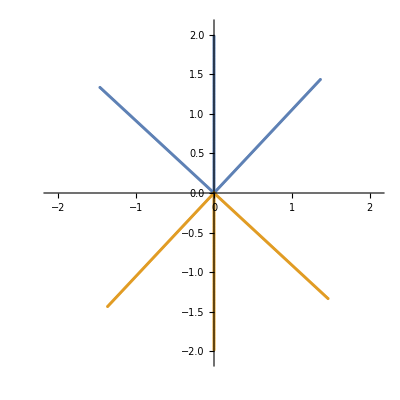

```mathematica
ListPlot[{randomregion,randomregionc},AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=1000;
```

```mathematica
α=GoldenRatio;
klist=Table[i,{i,α/20,40α,α/20}];
```

```mathematica
Do[

puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,klist[[j]],kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[klist[[j]]],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];

puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,klist[[j]],kicks]],{i,randomregionc}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregionc]*(kicks+1),2}];
poincareb=Graphics[{PointSize[0.0010],Red,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[klist[[j]]],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];

Export["poincare_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[klist[[j]]]]<>"_kicks_"<>ToString[kicks]<>"_frame"<>ToString[j]<>".png",Show[{poincarea,poincareb}]];
,{j,Length[klist]}]
```

$Aborted

```mathematica
filteredinitial//Length
```

103

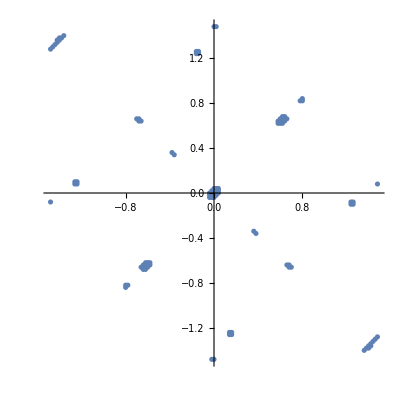

```mathematica
ListPlot[filteredinitial,AspectRatio->1]
```

```mathematica
α=GoldenRatio;
k=20.;
kicks=2000;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,filteredinitial}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[20.],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_filtered_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[20.]]<>"_kicks_"<>ToString[kicks]<>"_frameb"<>ToString[248]<>".png",poincarea];
```

## Powers of Poincaré

```mathematica
Clear[Fun];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];
(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a},
a=F[α,k,point];
MatrixPower[a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b},
a=F[α,k,point];
b=F[α,k,a.point];
MatrixPower[b.a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b,c},
a=F[α,k,point];
b=F[α,k,a.point];
c=F[α,k,b.(a.point)];
MatrixPower[c.b.a.mat,p].s
];*)

Clear[mapeop];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funp[α,k,#,p]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];*)
circlePoints=Select[gridPoints,Norm[#]<radius&];
(*randomregion=Join[boundaryPoints,circlePoints];
randomregionb=-randomregion;*)
randomregion=circlePoints;
randomregion//Length
```

20071

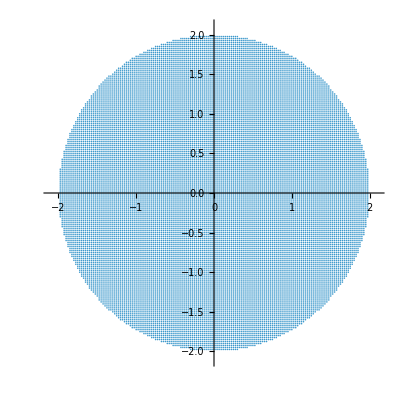

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=100;
k=20.;
p=1000;
```

```mathematica
puntosa=ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
```

```mathematica
Export["poincaretestb.csv",newpoincarea]
```

poincaretestb.csv

```mathematica
Export["poincaretestb.dat",newpoincarea]
```

$Aborted

```mathematica
Export["poincaretestb.m",newpoincarea]
```

poincaretestb.m

```mathematica
poincarec=Graphics[{PointSize[0.001],Blue,Opacity[0.01],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black],Style[", n = ",45,Black],Style[kicks,50,Black],Style[", p = ",45,Black],Style[p,50,Black]}],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_period_3_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>"_p_"<>ToString[p]<>"c.png",poincarec];
```

## Partial plots

```mathematica
newpoincarea//Length
```

2027171

```mathematica
plot=DensityHistogram[newpoincarea,400,PlotRange->All,ColorFunction->"TemperatureMap",PlotTheme->"Detailed",ImageSize->1000]
```

```mathematica
Export["test.png",plot,ImageSize->1000,ImageResolution->400]
```

test.png

## Symmetry lines

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
line=Table[{Rationalize[i],0},{i,-1.999,1.999,0.00025}];
sym=Table[rot[α/2].i,{i,line}];
sym=Join[sym,Table[rot[Pi/2].i,{i,sym}]];
sym//Length
```

31986

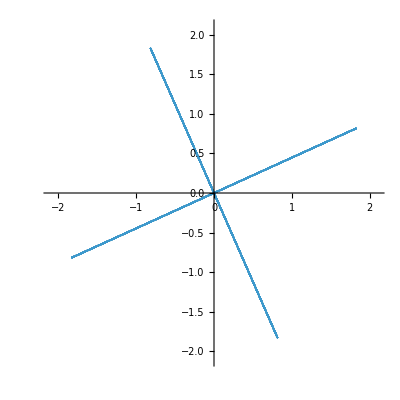

```mathematica
ListPlot[sym,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
k=20.;
```

```mathematica
nlist=Range[20];
```

```mathematica
Do[

puntosa=ParallelTable[Quiet[mapeo[i,α,k,n]],{i,sym}];
newpoincarea=ArrayReshape[puntosa,{Length[sym]*(n+1),2}];
symmetries=Graphics[{PointSize[0.0015],Red,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["symmetry_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_n_"<>ToString[n]<>"_frame"<>ToString[n]<>".png",symmetries];

,{n,nlist}]
```

```mathematica
n=5;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,n]],{i,N[sym]}];
newpoincarea=ArrayReshape[puntosa,{Length[sym]*(n+1),2}];
symmetries=Graphics[{PointSize[0.0015],Red,Opacity[0.3],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["testsymmetry_k_"<>ToString[N[k]]<>".png",symmetries]
```

testsymmetry_k_20..png

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.999],400];
```

```mathematica
k=20.;
kicks=1000;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincare=Graphics[{PointSize[0.0015],Gray,Opacity[0.2],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
```

```mathematica
Export["test.png",Show[{symmetries,poincare},PlotRange->{{-2.1,2.1},{-2.1,2.1}}]]
```

test.png